```mathematica
(*Standard Bethe ansatz definition t_nm=2 Min(m,n)-\delta_mn *)
t[i_,j_]:=2.Min[i,j]-1.KroneckerDelta[i,j];

(*Upper bound for string Bethe-Takahashi numbers *)
UpB[L_,M_,α_,n_]:=(L-1.-Sum[t[n,j]α[[j]],{j,1.,M}])/2.;

(* Select a Bethe-Takahashi number configuration at random *)
BTsel[M_,L_,α_]:=Block[{J,n,k},
J=Table[RandomSample[Table[k,{k,-UpB[L,M,α,n],
UpB[L,M,α,n]}],α[[n]]],{n,1,M}];J];

(* Scattering phases for the Bethe-Takahashi equations *)
Theta[x_,m_,n_]:=If[n!=m,2ArcTan[x/Abs[n-m]]+
4Sum[ArcTan[x/(Abs[n-m]+k)],{k,2,n+m-Abs[n-m]-2,2}]
+2ArcTan[x/(n+m)],4Sum[ArcTan[x/k],{k,2,2n-2,2}]+
2ArcTan[x/(2n)]];

(* Select the number of down spins M with probability *)
(* (Binomial[L,M]-Binomial[L,M-1])/Binomial[L,L/2] *)
choM[L_]:=Block[{a,p,check},
check=0;
While[check==0,
a=RandomInteger[{0,L/2}];
p=RandomReal[{0,1}];
If[p<=(Binomial[L,a]-Binomial[L,a-1])/(Binomial[L,L/2]),
check=1;];];a];

(* Generate a random string (uniformly distributed) using the *)
(* integer partitions of M *)
GenString[M_]:=Block[{part,part1,pair,d,j,k,m,p,
check},
m=M;
part=Reap[While[m!=0,
d=IntegerPart[RandomReal[{1.,M+1-10^(-12)}]];
j=IntegerPart[RandomReal[{1.,M+1-10^(-12)}]];
p=RandomReal[{0,1}];

If[p<=Re[(d PartitionsP[m-j d])/(m PartitionsP[m])],
Sow[Table[d,{k,1,j}]];
m=m-j d;];];][[2]];

(* Convert the partition to standard string format *)
part1=Flatten[part];
Table[Count[part1,i],{i,1,M}]];

ChooString[M_,L_]:=Block[{string,mat,DDol,DDne,i,j,
strNe,p,vec,vec1},
mat=Table[t[i,j],{i,1,M},{j,1,M}];
check=1;
While[check==1,
strNe=GenString[M];
DDne=Product[Binomial[L-Total[Table[mat[[i,j]]strNe[[j]],
{j,1,M}]],strNe[[i]]],{i,1,M}];
p=RandomReal[{0,1}];
If[p<=Min[1,Re[DDne/(Binomial[L,M]-Binomial[L,M-1])]],string=strNe;check=0;];];
string];
(* Metropolis step to accept a Bethe Takashi quantum numbers *)
(* configuration *)
Metropolis[Mo_,Mn_,Eo_,En_,L_,β_]:=Block[{p},
p=RandomReal[{0.,1.}];

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
If[p<=Min[1.,Abs[(L-2.Mn+1.)/(L-2.Mo+1.)Exp[-β[[1]](En[[1]]-Eo[[1]])-β[[2]](En[[2]]-Eo[[2]])-β[[3]](En[[3]]-Eo[[3]])-β[[4]](En[[4]]-Eo[[4]])]]],1,0]
];

Metro=Compile[{Mo,Mn,Eo,En,L,β},
Metropolis[Mo,Mn,Eo,En,L,β],CompilationTarget:>"C"];

(* Solve the Bethe-Takahashi equations for a given string *)
(* configuration "string" and Bethe-Takahashi numbers "BN" *)

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
SolveBethe[M_,L_,string_,BN_]:=Block[{sol,x,n,g,b,m,o,h,check,sol1,bit,EE,EE1,EE2,EE3},
check=1;
bit=0;
sol=Table[x[n][g],{n,1,M},{g,1,string[[n]]}]/.FindRoot[
Flatten[Table[ArcTan[x[n][g]/n]-π BN[[n,g]]/L-1/(2L)
∑_(m=1)^M ∑_(b=1)^string[[m]] If[m!=n||b!=g,Theta[x[n][g]-x[m][b],m,n],
0]==0,{n,1,M},{g,1,string[[n]]}]],Flatten[Table[
{x[o][h],RandomReal[]},{o,1,M},{h,1,string[[o]]}],1],
WorkingPrecision->15,MaxIterations->200,AccuracyGoal->15]//
Quiet;

check=Flatten[Table[ArcTan[sol[[n]][[g]]/n]-π BN[[n,g]]/L-
1/(2L)∑_(m=1)^M ∑_(b=1)^string[[m]] If[m!=n||b!=g,Theta[sol[[n]][[g]]-
sol[[m]][[b]],m,n],0],{n,1,M},{g,1,string[[n]]}]];
If[Total[Abs[check]]>10^-10,Print["Findroot failed with string"];
Print[BN];
bit=1;];
EE=If[M!=0,(*L/4.*)-Total[Flatten[Table[2.n/((sol[[n,g]])^2.+n^2.),
{n,1,M},{g,1,string[[n]]}]]],L/4.];

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
EE1=-Total[Flatten[Table[4.n*sol[[n,g]]/((sol[[n,g]])^2.+n^2.)^2,
{n,1,M},{g,1,string[[n]]}]]];
EE2=Total[Flatten[Table[2.n*(n^2-3*(sol[[n,g]])^2)/((sol[[n,g]])^2.+n^2.)^3,
{n,1,M},{g,1,string[[n]]}]]];
EE3=Total[Flatten[Table[8.n*sol[[n,g]]*(n^2-(sol[[n,g]])^2)/((sol[[n,g]])^2.+n^2.)^4,
{n,1,M},{g,1,string[[n]]}]]];
Flatten[{bit,EE,EE1,EE2,EE3,Chop[sol]}]
];

(* Inizialization from the ground state sector β is the *)
(* temperature *)
L=8;
Mo=L/2;
MCS=10000;
tsweeps=1000;

(*Demon update*)
EDD={};
DE=.1;
CDemon[Eo_,enertemp_]:=Block[{check},
DCEmax=.1;
check=0;
If[Chop[enertemp-Eo]≤ 0,
If[Abs[enertemp-Eo]≤ DCEmax,
DE=DE+Abs[Eo-enertemp];
check=1;
];,
If[Abs[enertemp-Eo]≤ DE,
DE=DE-Abs[enertemp-Eo];
check=1;,
];
];
{check,DE}
];

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
β={SetPrecision[1./1.0,30],SetPrecision[0.,30],SetPrecision[0.,30],SetPrecision[0.,30]};
strNe=ChooString[Mo,L];
BTnum=SetPrecision[BTsel[Mo,L,strNe],30];
sol=SolveBethe[Mo,L,strNe,BTnum];
(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
Eo={sol[[2]],sol[[3]],sol[[4]],sol[[5]]};

(* Metropolis update *)
BNumberst=BTnum;
Strconf=strNe;
Rap=sol;
i=1;

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
Monitor[data=Reap[
While[i<=MCS+tsweeps,
AppendTo[EDD,DE];
Mn=choM[L];
stringn=ChooString[Mn,L];
BTNn=SetPrecision[BTsel[Mn,L,stringn],30];

(*Reordering of the Bethe-Takahashi quantum numbers*)
BTNn1=Table[Sort[BTNn[[l]]],{l,1,Length[BTNn]}];
If[Mn!=0,
sol=SolveBethe[Mn,L,stringn,BTNn1];];
bit=sol[[1]];
(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
enertemp={sol[[2]],sol[[3]],sol[[4]],sol[[5]]};
(*Print[{Eo[[1]],enertemp[[1]],CDemon[Eo[[1]],enertemp[[1]]]}];*)
If[Mn==0, bit=0;enertemp={0,0,0,0};];
xxx=CDemon[Eo[[1]],enertemp[[1]]];

If[bit==0 && (*Metropolis[Mo,Mn,Eo,enertemp,L,β]*)xxx[[1]]==1,
DE=xxx[[2]];
(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
Eo={enertemp[[1]],enertemp[[2]],enertemp[[3]],enertemp[[4]]};
Mo=Mn;
Rap=sol;
BNumberst=BTNn1;
Strconf=stringn;
];

If[bit==0 &&i>tsweeps,
Sow[{Strconf,BNumberst,Rap,Chop[{Eo[[1]],Eo[[1]]^2,Eo[[2]],Eo[[2]]^2,Eo[[3]],Eo[[3]]^2,Eo[[4]],Eo[[4]]^2,N[Sum[(2k)/(L-2Mo+1),{k,-L/2+Mo,L/2-Mo}],8],N[Sum[(2k)^2/(L-2Mo+1),{k,-L/2+Mo,L/2-Mo}],8]}]}]
]
i++;];][[2]];

(*Restyling of Bethe numbers and rapidities*)
data1=Flatten[data,1];
Strconf=Table[data1[[i,1]],{i,1,Length[data1]}];
BNumbers=Table[Flatten[data1[[i,2]]],{i,1,Length[data1]}];
Rapidities=Table[data1[[i,3]],{i,1,Length[data1]}];
Obs=Table[data1[[i,4]],{i,1,Length[data1]}];

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
filename=StringJoin["/scratch/valba/GGE/CD_Rap_L",ToString[L],"beta[1]",ToString[N[β[[1]],3]],"beta[2]",ToString[N[β[[2]],3]],"beta[3]",ToString[N[β[[3]],3]],"beta[4]",ToString[N[β[[4]],3]],".dat"];
filename1=StringJoin["/scratch/valba/GGE/CD_StrConf_L",ToString[L],"beta[1]",ToString[N[β[[1]],3]],"beta[2]",ToString[N[β[[2]],3]],"beta[3]",ToString[N[β[[3]],3]],"beta[4]",ToString[N[β[[4]],3]],".dat"];
filename2=StringJoin["/scratch/valba/GGE/CD_Bnum_L",ToString[L],"beta[1]",ToString[N[β[[1]],3]],"beta[2]",ToString[N[β[[2]],3]],"beta[3]",ToString[N[β[[3]],3]],"beta[4]",ToString[N[β[[4]],3]],".dat"];
filename3=StringJoin["/scratch/valba/GGE/CD_Obs_L",ToString[L],"beta[1]",ToString[N[β[[1]],3]],"beta[2]",ToString[N[β[[2]],3]],"beta[3]",ToString[N[β[[3]],3]],"beta[4]",ToString[N[β[[4]],3]],".dat"];
Export[filename,Rapidities];
Export[filename1,Strconf];
Export[filename2,BNumbers];
Export[filename3,Obs];,i]

















(*M=4;
conf={};
count={};
max=1000;
For[ i=1,i≤max, i++,
st=ChooString[M,L];
If[!MemberQ[conf,st],AppendTo[conf,st];AppendTo[count,1/max],
pos=Flatten[Position[conf,st]];
count[[pos]]=count[[pos]]+1/max;
];
]

expct={};
mat=Table[t[i,j],{i,1,M},{j,1,M}];
For[k=1,k≤Length[conf],k++,
strNe=conf[[k]];
prob=Product[Binomial[L-Total[Table[mat[[i,j]]strNe[[j]],
{j,1,M}]],strNe[[i]]],{i,1,M}];
AppendTo[expct,prob/(Binomial[L,M]-Binomial[L,M-1])];
];

conf={};
count={};
For[ i=1,i≤max, i++,
st=BTsel[M,L,{2,1,0,0}];
If[!MemberQ[conf,st],AppendTo[conf,st];AppendTo[count,1/max],
pos=Flatten[Position[conf,st]];
count[[pos]]=count[[pos]]+1/max;
];
]
conf
N[count]*)
```

```mathematica
ChooString[0,L]
```

{}

```mathematica
CDemon[1,2,1]
```

CDemon[1,2,1]

```mathematica
(*Demon update*)
DE=5;
CDemon[Eo_,enertemp_]:=Block[{check,DCEmax},
DCEmax=10000;
check=0;
If[Chop[enertemp-Eo]≤  0,
If[Abs[enertemp-Eo]≤ DCEmax,
DE=DE+Eo-enertemp;
check=1;
];,
If[Chop[enertemp-Eo]≤ DE,
DE=DE-enertemp+Eo;
check=1;
];
];
check
];
```

```mathematica
DE=10;
CDemon[4.6928932188134526,0]
DE
```

1

14.6929

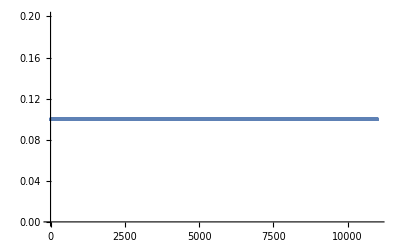

```mathematica
EDD//ListPlot
```

```mathematica
xxx
```

{0,0.1}